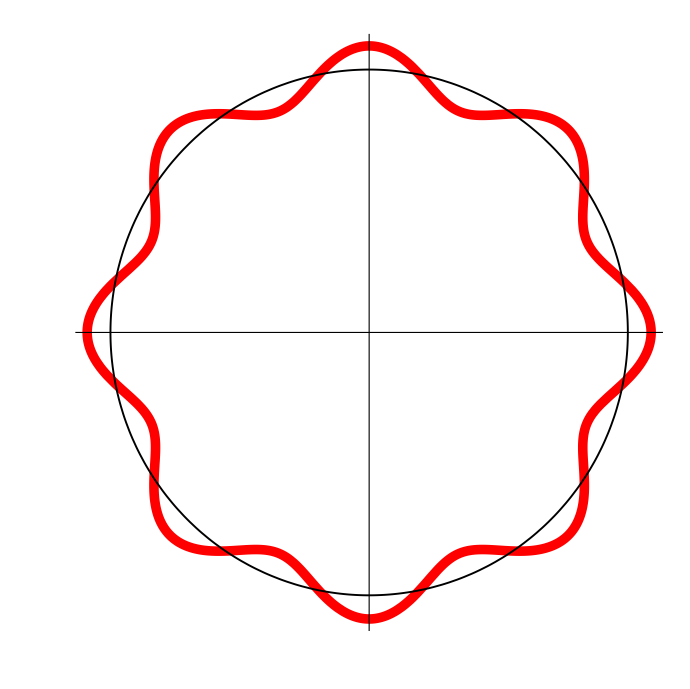

```mathematica
PolarPlot[{20+1.8*Cos[8*t],20},{t,0,2*Pi},PlotStyle->{{Red,Thickness[.01]},{Thickness[.002],Black}},Axes->{False,True},Ticks->False]
```

```mathematica
z1=BesselJPrimeZeros[4,1]
```

{5.31755}

```mathematica
RevolutionPlot3D[BesselJ[4,z1[[1]]*r]*Cos[4*θ],{r,0,1},{θ,0,2*Pi},Axes->False,Boxed->False,Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Export["/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/cylinderphi.png",-Graphics3D-,Background->None]
```

/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/cylinderphi.png

```mathematica
z2=BesselJPrimeZeros[0,4]
z3=BesselJPrimeZeros[1,4]
```

{3.83171,7.01559,10.1735,13.3237}

{1.84118,5.33144,8.53632,11.706}

```mathematica
z2=Prepend[z2,0]
```

{0,3.83171,7.01559,10.1735,13.3237}

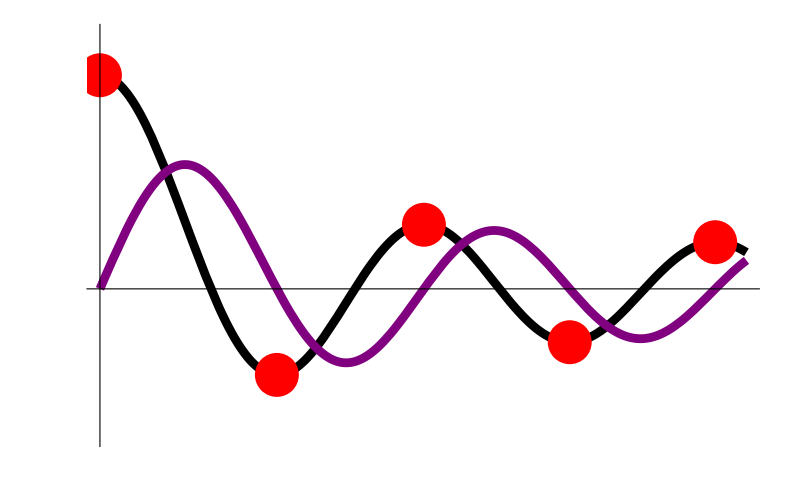

```mathematica
img1=Plot[{BesselJ[0,r],BesselJ[1,r]},{r,0,14},PlotStyle->{{Black,Thickness[.008]},{Purple,Thickness[.008]}},Ticks->False,PlotRange->{-.7,1.2},Epilog->{PointSize[.04],Red,Point[Table[{z2[[k]],BesselJ[0,z2[[k]]]},{k,1,5}]]}]
```

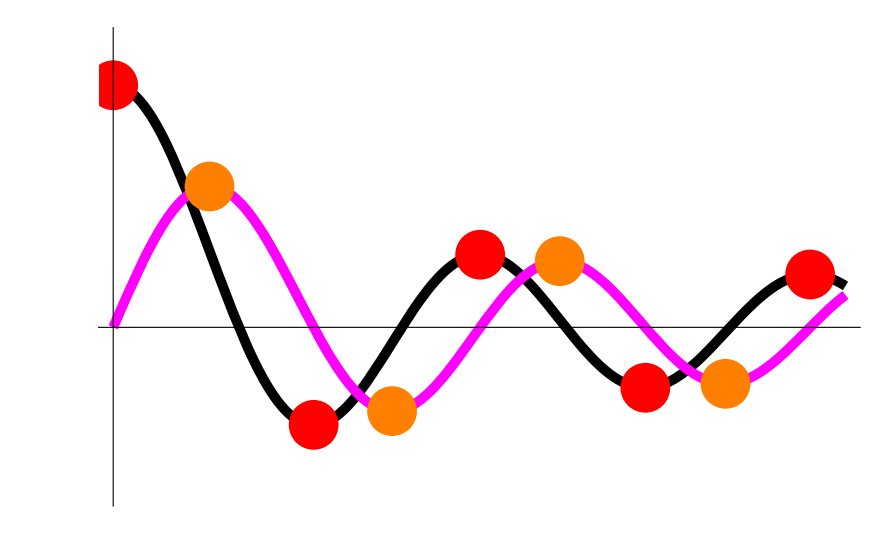
```mathematica
Export["/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/besselprimezeros.png",-Graphics-,Background->None]
```

/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/besselprimezeros.png

```mathematica
img1=Plot[{BesselJ[0,r],BesselJ[1,r]},{r,0,14},PlotStyle->{{Black,Thickness[.008]},{Magenta,Thickness[.008]}},Ticks->False,PlotRange->{-.7,1.2},Epilog->{{PointSize[.04],Red,Point[Table[{z2[[k]],BesselJ[0,z2[[k]]]},{k,1,5}]]},{PointSize[.04],Orange,Point[Table[{z3[[k]],BesselJ[1,z3[[k]]]},{k,1,4}]]}}]
```

-Graphics-

```mathematica
z4=BesselJZeros[0,4]
z5=BesselJZeros[25/48,4]
```

{2.40483,5.52008,8.65373,11.7915}

{3.1711,6.31425,9.45638,12.5983}

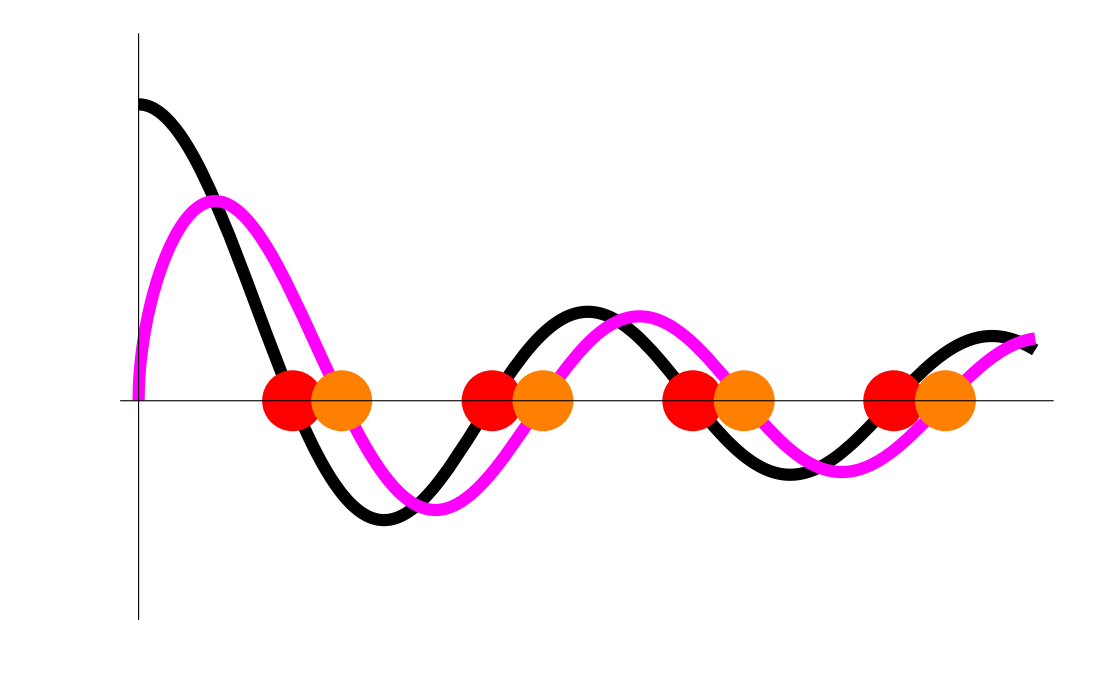

```mathematica
img2=Plot[{BesselJ[0,r],BesselJ[25/48,r]},{r,0,14},PlotStyle->{{Black,Thickness[.008]},{Magenta,Thickness[.008]}},Ticks->False,PlotRange->{-.7,1.2},Epilog->{{PointSize[.04],Red,Point[Table[{z4[[k]],BesselJ[0,z4[[k]]]},{k,1,4}]]},{PointSize[.04],Orange,Point[Table[{z5[[k]],BesselJ[25/48,z5[[k]]]},{k,1,4}]]}}]
```

```mathematica
Export["/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/besselzeros.png",img2,Background->None]
```

/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/besselzeros.png

```mathematica
imglist=Table[RevolutionPlot3D[Sin[allZeros[[l]][[1]]*(ϕ-β)]*BesselJ[allZeros[[l]][[1]],allZeros[[l]][[3]]*r],{r,0,atymp},{ϕ,β,2*Pi-β},Axes->False,Boxed->False,Mesh->None,ColorFunction->"Rainbow"],{l,1,4}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[Export["/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/membmode"<>ToString[l]<>".png",imglist[[l]],Background->None],{l,1,4}]
```

{/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/membmode1.png,/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/membmode2.png,/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/membmode3.png,/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/membmode4.png}

```mathematica
Export["/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/membmode"<>ToString[3]<>".png",imglist[[3]],Background->None]
```

/home/t35-room3023/Documents/ICE-Model/Thesis - Presentation/Thesis/Draft/LaTeXVorlage/Diagrams/Presentation/BoundaryConditions/membmode3.png

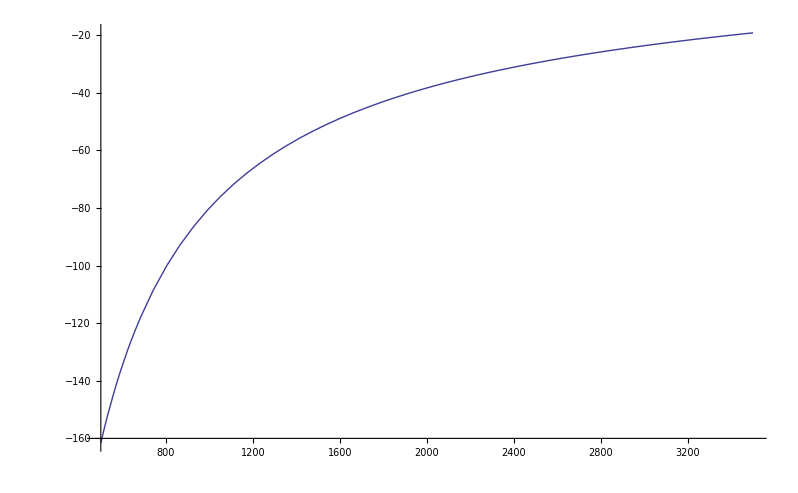

```mathematica
Plot[{Gamplus},{f,fmin,fmax}]
```

```mathematica
N[c/(2*L)]
```

7795.45